```mathematica
(* https://github.com/shahin-mansouri *)
```

```mathematica
f[x_, y_]=x + y;
```

```mathematica
steps = 100;
x[0] = 1;
y[0] = 1;
xStop = 1.6;
h = (xStop - x[0])/steps
```

0.006

```mathematica
i = 0;
While[x[i] < xStop,
i=i+1;
x[i] = x[i-1] + h;
y[i]= Expand[y[i-1] + h f[x[i], y] - y];
y[i]=NSolve[y[i]==0];
y[i] = y[i][[1, 1, 2]];
]
```

```mathematica
x = Table[x[n], {n,0, i}]
```

```mathematica
y = Table[y[n], {n, 0, i}]
```

```mathematica
xy = Table[{x[[n]], y[[n]]}, {n, 0, i}]
```

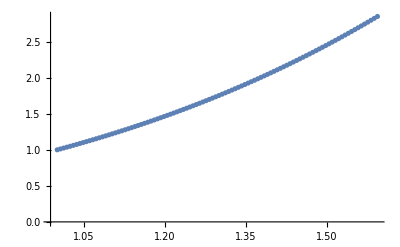

```mathematica
ListPlot[xy]
```